```mathematica
Begin["BoatContext`"];
NotebookDirectory["/home/wolf/qea"];
libboatLocation="/home/wolf/qea/libboat.nb";
libboat=NotebookOpen[libboatLocation];
SelectionMove[libboat,All,Notebook];
SelectionEvaluate[libboat];
```

```mathematica
bHullFileLocation="/home/wolf/qea/hulls/boats/bestlemon.stl";
hullFileLocation="/home/wolf/qea/final-boat/bestlemonhotel-bailed.stl";
(*hullFileLocation="tmp.stl";*)

canFileLocation="/home/wolf/qea/parts/can.stl";
can=Import[canFileLocation,"BoundaryMeshRegion"];

mastFileLocation="/home/wolf/qea/parts/mast.stl";
mast=Import[mastFileLocation,"BoundaryMeshRegion"];

(* Convert from STL file units to cm *)
stlUnits="Meters";
stlScale=QuantityMagnitude[UnitConvert[stlUnits,Quantity[, "Centimeters"]]];

yScale=1;
zScale=1;

(* Generate point cloud *)
buoyHullNonScaled=Import[bHullFileLocation,"BoundaryMeshRegion"];
buoyHull=TransformedRegion[buoyHullNonScaled,ScalingTransform[{stlScale,stlScale*yScale,stlScale*zScale}]];
(*buoyHull=Import["hulls/cube/cube.stl","BoundaryMeshRegion"];*)
buoyHullVolume=Volume[buoyHull]Quantity[, ("Centimeters")^3];
buoyHullPoints=pointCloud[buoyHull,1000000];
buoyHullCentroid=RegionCentroid[buoyHull];

hullNonScaled=Import[hullFileLocation,"BoundaryMeshRegion"];
hull=TransformedRegion[hullNonScaled,ScalingTransform[{stlScale,stlScale*yScale,stlScale*zScale}]];
(*hull=Import["hulls/cube/cube.stl","BoundaryMeshRegion"];*)
hullVolume=Volume[buoyHull]Quantity[, ("Centimeters")^3];
hullCentroid=RegionCentroid[hull];

(* Constants *)
(*GeogravityModelData[CityData[Entity["City",{"Needham","Massachusetts","UnitedStates"}],"Coordinates"],"Magnitude"];*)
g=9.81 Quantity[, ("Meters")/("Seconds")^2];
blueFoamDensity=0.0317 Quantity[, ("Grams")/("Centimeters")^3];
waterDensity=1 Quantity[, ("Grams")/("Centimeters")^3];
```

```mathematica
canLocs=canLocationFinder[buoyHullCentroid,8,-3.6-0.2+.5];
can1Loc=canLocs[[1]];
can2Loc=canLocs[[2]];

mastLoc=mastLocationFinder[buoyHullCentroid,25-8.5];

ballast1=ballastLocationFinder[buoyHullCentroid,-12];
ballast2=ballastLocationFinder[buoyHullCentroid,-9];
ballast3=ballastLocationFinder[buoyHullCentroid,-9];

frontVec=Normalize[{1,0,0}];
boat={
<|
name->"BuoyHull",
type->"Buoy",
mass->buoyHullVolume*waterDensity,
volume->buoyHullVolume,
points->buoyHullPoints,
region->buoyHull,
render->{GraphicsComplex[MeshCoordinates@buoyHull,MeshCells[buoyHull,2]]},
cobRender->({White,PointSize[Large],Point[#]}&)
|>,
<|
name->"Hull",
type->"PointMass",
mass->hullVolume*blueFoamDensity,
volume->hullVolume,
com->Quantity[hullCentroid,"Centimeters"],
render->{
{Black,PointSize[Large],Point[hullCentroid]},
{EdgeForm[],Opacity[.6],LightPink,GraphicsComplex[MeshCoordinates@hull,MeshCells[hull,2]]}
}
|>,
<|
name->"Can",
type->"PointMass",
mass->389.5 Quantity[, "Grams"],
com->Quantity[can1Loc,"Centimeters"],
render->{
{Black,PointSize[Large],Point[can1Loc]},
{EdgeForm[],Opacity[.6],LightGray,Translate[GraphicsComplex[MeshCoordinates@can,MeshCells[can,2]],can1Loc]}
}
|>,
<|
name->"Can",
type->"PointMass",
mass->389.5 Quantity[, "Grams"],
com->Quantity[can2Loc,"Centimeters"],
render->{
{Black,PointSize[Large],Point[can2Loc]},
{EdgeForm[],Opacity[.6],LightGray,Translate[GraphicsComplex[MeshCoordinates@can,MeshCells[can,2]],can2Loc]}
}
|>,
<|
name->"Mast",
type->"PointMass",
mass->96.2 Quantity[, "Grams"],
com->Quantity[mastLoc,"Centimeters"],
render->{
{Black,PointSize[Large],Point[mastLoc]},
{EdgeForm[],Opacity[.6],LightGray,Translate[GraphicsComplex[MeshCoordinates@mast,MeshCells[mast,2]],mastLoc]}
}
|>(*,
<|
name->"Ballast",
type->"PointMass",
mass->100Quantity[, "Grams"],
com->Quantity[ballast1,"Centimeters"],
render->{
{Black,PointSize[Large],Point[ballast1]}
}
|>,
<|
name->"Ballast",
type->"PointMass",
mass->100Quantity[, "Grams"],
com->Quantity[ballast2,"Centimeters"],
render->{
{Black,PointSize[Large],Point[ballast1]}
}
|>,
<|
name->"Ballast",
type->"PointMass",
mass->100Quantity[, "Grams"],
com->Quantity[ballast3,"Centimeters"],
render->{
{Black,PointSize[Large],Point[ballast1]}
}
|>*)
};

GraphicsGrid[{
{Show[renderBoat[boat,Normalize[{0,0,1}]],ViewPoint->{0,-∞,0}],
Show[renderBoat[boat,Normalize[{0,0,1}]],ViewPoint->{∞,0,0}]},
{Show[renderBoat[boat,Normalize[{0,0,1}]],ViewPoint->{0,0,∞}],
Show[renderBoat[boat,Normalize[{0,0,1}]],ViewPoint->{1.3, -2.4, 2.}]}
},ImageSize->Full]
exportBoat[boat,bHullFileLocation,"boat.json"]
```

-Graphics-

boat.json

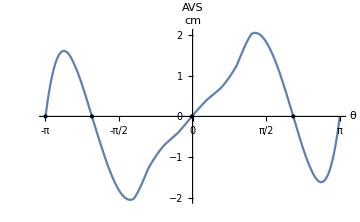
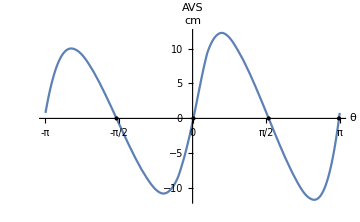
Boat | -Graphics3D-
AVS Plot | -Graphics-
AVS Zeros | -179.901 ° | -123.179 ° | -0.869733 ° | 123.226 °
Trim AVS | -Graphics-
Trim | 1.04294 °

```mathematica
boatSummary[boat]
```

```mathematica
<|
name->"Ballast",
type->"PointMass",
mass->100 Quantity[, "Grams"],
com->Quantity[ballast1,"Centimeters"],
render->{
{Black,PointSize[Large],Point[ballast1]}
}
|>
```

```mathematica
UnitConvert[Plus@@calculateMoments[boat,Normalize[{0,1,0}]],"NewtonMeters"]
```

{-0.248474 m N,0. m N,0.0868367 m N}

```mathematica
"boat.json"
```

## Boats

```mathematica
renderBoat[boat,Normalize[{0,0,1}]]
```

-Graphics3D-

```mathematica
manyBoats[boat,10,FrontVec->{1,0,0},ViewPoint->{∞,0,0}]
```

LinkObject::linkd: Unable to communicate with closed link LinkObject["/usr/local/Wolfram/Mathematica/10.3/Executables/wolfram" -subkernel -noinit -wstp,2237,8].

Kernels::rdead: Subkernel connected through KernelObject[1,local] appears dead.

LinkObject::linkd: Unable to communicate with closed link LinkObject["/usr/local/Wolfram/Mathematica/10.3/Executables/wolfram" -subkernel -noinit -wstp,2238,9].

Kernels::rdead: Subkernel connected through KernelObject[2,local] appears dead.

LinkObject::linkn: Argument LinkObject["/usr/local/Wolfram/Mathematica/10.3/Executables/wolfram" -subkernel -noinit -wstp,2237,8] in LinkWrite[LinkObject["/usr/local/Wolfram/Mathematica/10.3/Executables/wolfram" -subkernel -noinit -wstp,2237,8],EvaluatePacket[{$KernelID,TimeUsed[]}]] has an invalid LinkObject number; the link may be closed.

Kernels::rdead: Subkernel connected through KernelObject[1,local] appears dead.

General::stop: Further output of Kernels::rdead will be suppressed during this calculation.

LinkObject::linkn: Argument LinkObject["/usr/local/Wolfram/Mathematica/10.3/Executables/wolfram" -subkernel -noinit -wstp,2238,9] in LinkWrite[LinkObject["/usr/local/Wolfram/Mathematica/10.3/Executables/wolfram" -subkernel -noinit -wstp,2238,9],EvaluatePacket[{$KernelID,TimeUsed[]}]] has an invalid LinkObject number; the link may be closed.

Interpreting unit ....

Interpreting unit ....

Interpreting unit ....

«8 more identical outputs»

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
N[Quantity[39.37, "Inches"]]
```

39.37 in

```mathematica
QuantityMagnitude[Quantity[39.37,"Inches"]]
```

39.37